```mathematica
CleanSlate[]
```

Remove::rmnsm: There are no symbols matching "const$".

Remove::rmnsm: There are no symbols matching "i$".

Remove::rmnsm: There are no symbols matching "resMat$".

General::stop: Further output of Remove::rmnsm will be suppressed during this calculation.

contexts purged: {Global`}

approximate kernel memory recovered: 316 Kb

{CleanSlate`,SymbolicMachineLearningLoader`,IconizeLoader`,HTTPHandlingLoader`,StreamingLoader`,CloudObjectLoader`,PacletManager`,System`,Global`}

```mathematica
This is a pinned-pinned flagpole.


Notation:nyp means _next y^(p), the next iteration of the p-th derivative of y,similarly pyp means _previous y^(p), the previous iteration value of the p-th derivative.
```

```mathematica
py0= a + b x + c x^2+d x^3+ e x^4
```

a+b x+c x^2+d x^3+e x^4

```mathematica
Solve[py0==0/.x->0]
```

{{a→0}}

```mathematica
Solve[py0==0/.{x->l, a->0}]
```

{{b→-c l-d l^2-e l^3},{l→0}}

```mathematica
py2=D[py0,{x,2}]
```

2 c+6 d x+12 e x^2

```mathematica
Solve[py2==0/.x->0]
```

{{c→0}}

```mathematica
Solve[py2==0/.{x->l, c->0}]
```

{{d→-2 e l},{l→0}}

```mathematica
Simplify[py0/.{a->0, b->-(-2 e l) l^2-e l^3,c->0, d->-2 e l}]
```

e x (l^3-2 l x^2+x^3)

```mathematica
Remove[a,b,c,d,py0, py2];
```

```mathematica
y0[x_]:=e x (l^3-2 l x^2+x^3)
```

```mathematica
e1y0[x_]:=x (l^3-2 l x^2+x^3)/.l->100
```

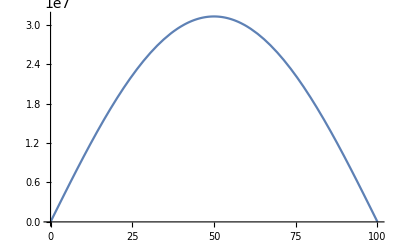

```mathematica
Plot[e1y0[x],{x,0,100}]
```

```mathematica
Thus, the initial shape is symmetric!Iterations should improve on this. Compute expr1y1 and expr1y2, which are needed to start the 1st iteration.
```

```mathematica
Define iteration function:
```

```mathematica
IteratePinnedPinnedFlagpole[No_, y0_]:= 
Module[{i,tmpy0,tmpy1,tmpy2, tmpy3, const,resMat},
resMat={{0,y0,Simplify[D[y0, {x, 1}]],Simplify[D[y0, {x, 2}]],Simplify[D[y0, {x, 3}]],Simplify[D[y0, {x, 4}]]}};
  For[i=2,i≤No,i++,
resMat=Append[resMat,{0,0,0,0,0,0}];
resMat[[i,6]]=Simplify[{w/EI(x-l)resMat[[i-1,4]] + w/EI resMat[[i-1,3]]}];(* Above the basic equation for a pinned-pinned "flagpole" *);
Clear[const];tmpy5 = Simplify[∫resMat[[i,6]]ⅆx + const];tmpy4=Simplify[∫tmpy5ⅆx];

const = Solve[-tmpy4[[1]]==0/.x->l, const][[1,1,2]];
resMat[[i,5]]=Simplify[tmpy5];
resMat[[i,4]]=Simplify[tmpy4];
Clear[const];tmpy3=Simplify[∫resMat[[i,4]]ⅆx+const];tmpy2 = Simplify[∫tmpy3ⅆx];const = Solve[-tmpy2[[1]]==0/.x->l, const][[1,1,2]];
resMat[[i,3]] = Simplify[tmpy3];resMat[[i,2]]=Simplify[tmpy2];

resMat[[i,1]] = N[Simplify[(l^3 w)/EI resMat[[i-1,3]]/resMat[[i,3]] /.x->l],5];
];
Return[resMat]
]
```

```mathematica
resMat=IteratePinnedPinnedFlagpole[9,y0[x]];
```

```mathematica
Flatten[resMat[[{1,2,3,4,5,6,7,8},1]]]
```

{0,22.703,19.11,18.669,18.589,18.573,18.57,18.569}

```mathematica
e2y0[x_]:=resMat[[2,2]]/.{e->1, w->1, EI->5 10^4, l->100}
e3y0[x_]:=resMat[[3,2]]/.{e->1, w->1, EI->5 10^4, l->100}
e4y0[x_]:=resMat[[4,2]]/.{e->1, w->1, EI->5 10^4, l->100}
e5y0[x_]:=resMat[[5,2]]/.{e->1, w->1, EI->5 10^4, l->100}
e6y0[x_]:=resMat[[6,2]]/.{e->1, w->1, EI->5 10^4, l->100}
e7y0[x_]:=resMat[[7,2]]/.{e->1, w->1, EI->5 10^4, l->100}
e8y0[x_]:=resMat[[8,2]]/.{e->1, w->1, EI->5 10^4, l->100}
```

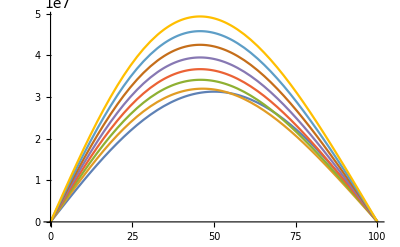

```mathematica
Plot[{e1y0[x], e2y0[x],e3y0[x], e4y0[x],e5y0[x], e6y0[x],e7y0[x], e8y0[x],},{x,0,100}]
```

```mathematica
Flatten[resMat[[{1,2,3,4,5,6,7,8},2]]]//MatrixForm
```

(e x (l^3-2 l x^2+x^3)
(e w x (47 l^6-112 l^4 x^2+35 l^3 x^3+84 l^2 x^4-70 l x^5+16 x^6))/(840 EI)
(e w^2 x (921 l^9-2310 l^7 x^2+705 l^6 x^3+2016 l^5 x^4-1428 l^4 x^5-480 l^3 x^6+900 l^2 x^7-380 l x^8+56 x^9))/(302400 EI^2)
(e w^3 x (1194621 l^12-3034668 l^10 x^2+921921 l^9 x^3+2774772 l^8 x^4-1951950 l^7 x^5-830544 l^6 x^6+1333332 l^5 x^7-248248 l^4 x^8-352352 l^3 x^9+257712 l^2 x^10-72436 l x^11+7840 x^12))/(7264857600 EI^3)
(e w^4 x (7724649 l^15-19680882 l^13 x^2+5973105 l^12 x^3+18208008 l^11 x^4-12791688 l^10 x^5-5820672 l^9 x^6+9137700 l^8 x^7-1404260 l^7 x^8-2746744 l^6 x^9+1563744 l^5 x^10+117208 l^4 x^11-444640 l^3 x^12+203520 l^2 x^13-42688 l x^14+3640 x^15))/(871782912000 EI^4)
(e w^5 x (338652666567 l^18-863390689560 l^16 x^2+261981470835 l^15 x^3+800972535636 l^14 x^4-562548552678 l^13 x^5-260264175120 l^12 x^6+406471681980 l^11 x^7-58148759760 l^10 x^8-128703246672 l^9 x^9+70493819760 l^8 x^10+9144162300 l^7 x^11-21187921440 l^6 x^12+5886558720 l^5 x^13+2142776832 l^4 x^14-2090520600 l^3 x^15+696175200 l^2 x^16-116135600 l x^17+8153600 x^18))/(709596419051520000 EI^5)
(e w^6 x (4814910584973 l^21-12277329717510 l^19 x^2+3725179332237 l^18 x^3+11396757102192 l^17 x^4-8003815494444 l^16 x^5-3717291970656 l^15 x^6+5798692424052 l^14 x^7-813707761548 l^13 x^8-1860328316616 l^12 x^9+1006696611648 l^11 x^10+152738725776 l^10 x^11-317302228320 l^9 x^12+80469480960 l^8 x^13+37247491776 l^7 x^14-28117162920 l^6 x^15+3252775680 l^5 x^16+3536714720 l^4 x^17-2056208000 l^3 x^18+537472320 l^2 x^19-74282560 l x^20+4426240 x^21))/(187333454629601280000 EI^6)
(e w^7 x (65126716642436193 l^24-166068969815938644 l^22 x^2+50388039271742445 l^21 x^3+154178706592490580 l^20 x^4-108276554665733454 l^19 x^5-50331349545686352 l^18 x^6+78492492162023940 l^17 x^7-10964254837415880 l^16 x^8-25259225101734624 l^15 x^9+13626802309406832 l^14 x^10+2146259869317564 l^13 x^11-4343625717254880 l^12 x^12+1062691772163840 l^11 x^13+548117018327424 l^10 x^14-392549752194600 l^9 x^15+34956815493600 l^8 x^16+51739523435600 l^7 x^17-21823004403200 l^6 x^18-307108401600 l^5 x^19+3233254344320 l^4 x^20-1354127465600 l^3 x^21+290948985600 l^2 x^22-34276205600 l x^23+1772266496 x^24))/(47050670464770657484800000 EI^7))

```mathematica
Flatten[resMat[[{1,2,3,4,5,6,7,8},3]]]//MatrixForm
```

(e (l^3-6 l x^2+4 x^3)
(e w (47 l^6-336 l^4 x^2+140 l^3 x^3+420 l^2 x^4-420 l x^5+112 x^6))/(840 EI)
(e w^2 (921 l^9-6930 l^7 x^2+2820 l^6 x^3+10080 l^5 x^4-8568 l^4 x^5-3360 l^3 x^6+7200 l^2 x^7-3420 l x^8+560 x^9))/(302400 EI^2)
(e w^3 (1194621 l^12+364 x^2 (-25011 l^10+10131 l^9 x+38115 l^8 x^2-32175 l^7 x^3-15972 l^6 x^4+29304 l^5 x^5-6138 l^4 x^6-9680 l^3 x^7+7788 l^2 x^8-2388 l x^9+280 x^10)))/(7264857600 EI^3)
(e w^4 (7724649 l^15-59042646 l^13 x^2+23892420 l^12 x^3+91040040 l^11 x^4-76750128 l^10 x^5-40744704 l^9 x^6+73101600 l^8 x^7-12638340 l^7 x^8-27467440 l^6 x^9+17201184 l^5 x^10+1406496 l^4 x^11-5780320 l^3 x^12+2849280 l^2 x^13-640320 l x^14+58240 x^15))/(871782912000 EI^4)
(e w^5 (37628074063 l^18+2660 (-108194322 l^16 x^2+43773011 l^15 x^3+167287497 l^14 x^4-(704948061 l^13 x^5)/5-76100636 l^12 x^6+135830136 l^11 x^7-21860436 l^10 x^8-(161282264 l^9 x^9)/3+32390644 l^8 x^10+4583540 l^7 x^11-(34516664 l^6 x^12)/3+3442432 l^5 x^13+1342592 l^4 x^14-(4191520 l^3 x^15)/3+494360 l^2 x^16-87320 l x^17+(58240 x^18)/9)))/(78844046561280000 EI^5)
(e w^6 (1604970194991 l^21+44 (-558060441705/2 l^19 x^2+112884222189 l^18 x^3+431695344780 l^17 x^4-363809795202 l^16 x^5-197129119656 l^15 x^6+351435904488 l^14 x^7-55480074651 l^13 x^8-140933963380 l^12 x^9+83891384304 l^11 x^10+(152738725776 l^10 x^11)/11-31249461880 l^9 x^12+8534641920 l^8 x^13+4232669520 l^7 x^14-3408140960 l^6 x^15+418918080 l^5 x^16+482279280 l^4 x^17-(887908000 l^3 x^18)/3+81435200 l^2 x^19-11817680 l x^20+(2213120 x^21)/3)))/(62444484876533760000 EI^6)
(e w^7 (21708905547478731 l^24+364 (-456233433560271 l^22 x^2+184571572423965 l^21 x^3+705946458756825 l^20 x^4-594926124536997 l^19 x^5-322636856062092 l^18 x^6+575036572615560 l^17 x^7-90364737671010 l^16 x^8-231311585180720 l^15 x^9+137266323629556 l^14 x^10+23585273289204 l^13 x^11-51709829967320 l^12 x^12+13624253489280 l^11 x^13+7529079922080 l^10 x^14-5751644720800 l^9 x^15+544199508600 l^8 x^16+852849287400 l^7 x^17-(1139112867200 l^6 x^18)/3-5624696000 l^5 x^19+62177968160 l^4 x^20-(81842868800 l^3 x^21)/3+6128046400 l^2 x^22-753323200 l x^23+(121721600 x^24)/3)))/(15683556821590219161600000 EI^7))